```mathematica
Needs["ErrorBarPlots`"]
```

# Simulated Histograms

```mathematica
ICEffArea = Import["/Users/carguelles/Dropbox/NuestrosProyectos/CJAtmSterile/c++/data/icecube_cw_effarea.dat"];
NuEnergy = Union[#⟦1⟧&/@ICEffArea];
CosTh = Union[(#⟦2⟧+0.05)&/@ICEffArea];
```

```mathematica
PlotZenithDistribution[data_,options___]:=ListPlot[MapThread[List,{CosTh,Total[data,{-1}]}],Frame->True,options];
PlotZenithDistributionError[data_,options___]:=ErrorListPlot[MapThread[List,{CosTh,Total[data,{-1}],Sqrt[Total[data,{-1}]]+0.15*Total[data,{-1}]}],Frame->True,options];
PlotEnergyDistribution[data_]:=ListLogLogPlot[MapThread[List,{NuEnergy,MapThread[Plus,data]}],Frame->True];
PlotAllEnergyDistribution[data_,options___]:=ListLogLogPlot[MapThread[List,{NuEnergy,#}],Frame->True,options]&/@data;
```

```mathematica
MeanEnergy[data_]:=NuEnergy[[Position[(#⟦1⟧<0.5 && #[[2]]>0.5)&/@Partition[N[#/Total[data,∞]&/@Drop[FoldList[Plus,0,MapThread[Plus,data]],1]],2,1],True][[1]][[1]]]]
```

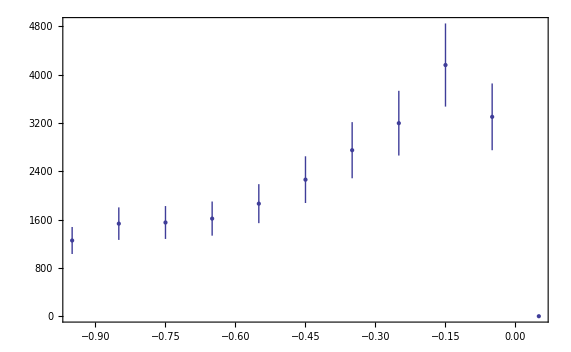

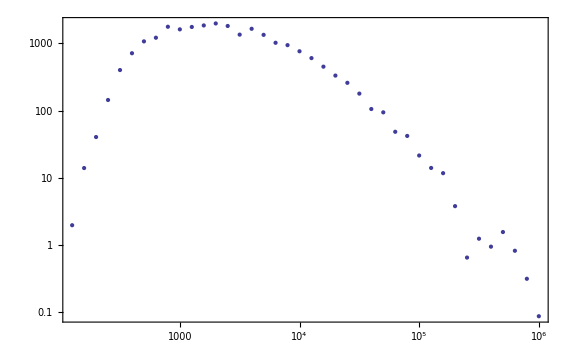

```mathematica
FS=Import["/Users/carguelles/Dropbox/NuestrosProyectos/CJAtmSterile/sim_data/simdata_0_0.dat"];
PlotZenithDistributionError[FS,PlotRange->All]
PlotEnergyDistribution[FS]
```

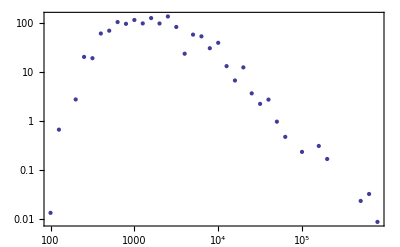
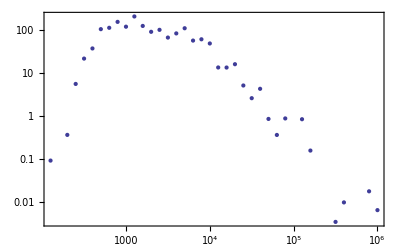
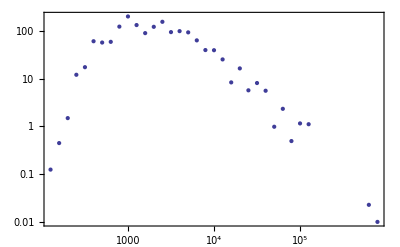
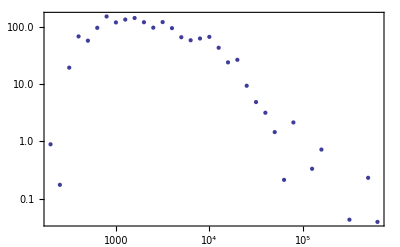
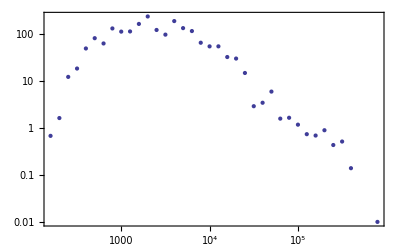
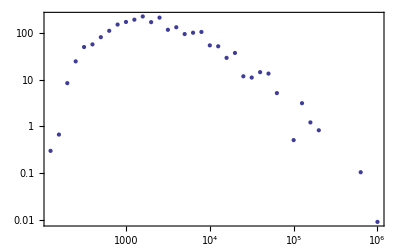
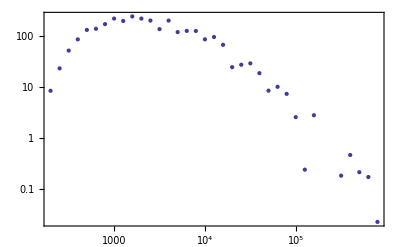
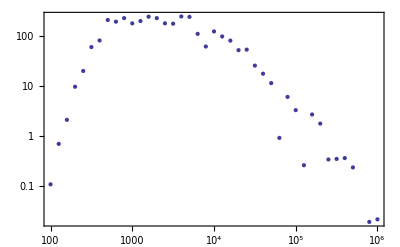
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotAllEnergyDistribution[FS]
```

```mathematica
STD=Import["/Users/carguelles/Dropbox/NuestrosProyectos/CJAtmSterile/sim_data/sim_0_0.dat"];
SIM=Import["/Users/carguelles/Dropbox/NuestrosProyectos/CJAtmSterile/sim_data/sim_0.158489_0.49993.dat"];
```

```mathematica
Total[FS,∞]/Total[STD,∞]
```

0.978853

```mathematica
HistogramList
```

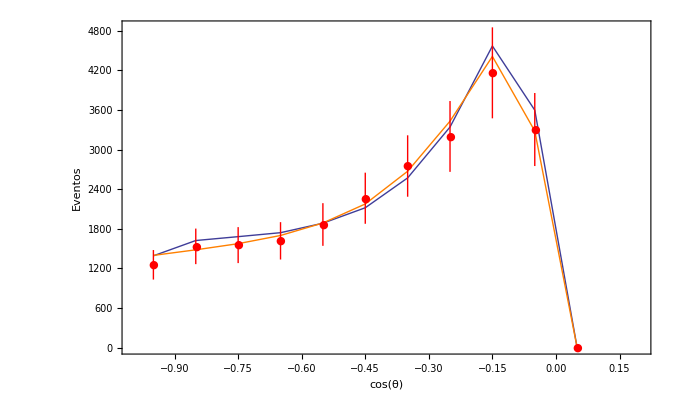

```mathematica
Show[PlotZenithDistribution[SIM,Joined->True,PlotStyle->{Thick}],
PlotZenithDistribution[STD,Joined->True,PlotStyle->{Orange,Thick}],PlotZenithDistributionError[FS,PlotStyle->{Thick,Red},PlotMarkers->{Automatic,Medium}],PlotRange->{{-1.,0.2},All},FrameStyle->Thick,FrameTicksStyle->Directive[15],FrameLabel->{"cos(θ)","Eventos"},LabelStyle->Large]
```

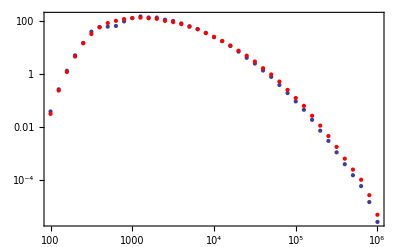
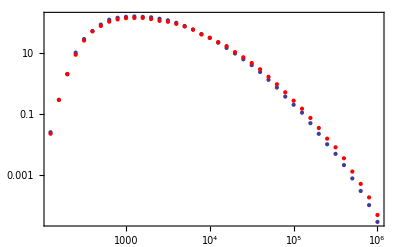
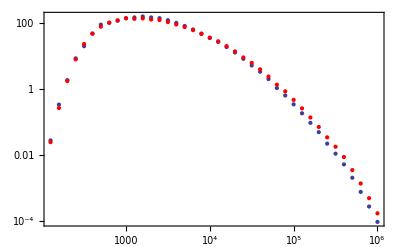
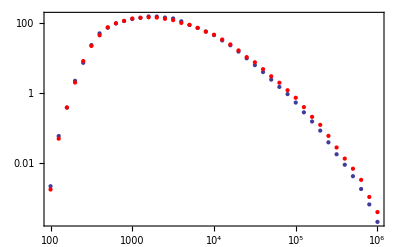
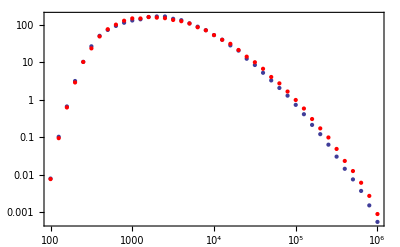
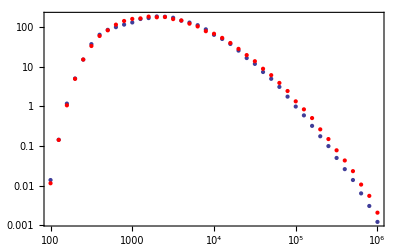
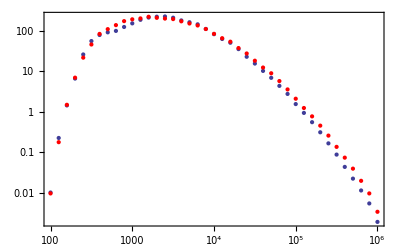
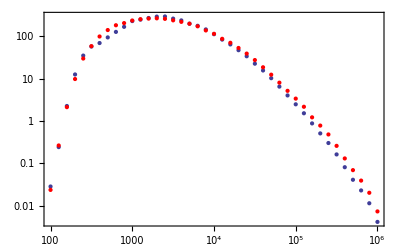
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MapThread[Show[#1,#2, PlotRange->All]&,{PlotAllEnergyDistribution[SIM],PlotAllEnergyDistribution[STD,PlotStyle->{Red}]}]
```

# Results from CONDOR

```mathematica
path = "/Users/carguelles/Dropbox/NuestrosProyectos/CJAtmSterile/results/";
RawDataImport=Import[path<>"outvalues_1.dat","Data"];
```

```mathematica
DataSelect={#⟦4⟧,#⟦5⟧,#⟦3⟧}&/@RawDataImport;
sin2sqValues = 
Log10[Sin[2.0*DeleteDuplicates[#[[2]]&/@DataSelect]]^2];
dmsqValues = Log10[DeleteDuplicates[#[[1]]&/@DataSelect]];
```

```mathematica
Operation[data_,i_]:=Module[{},
{Log10[Sin[2.0*#⟦5⟧]^2],Log10[#⟦4⟧],#[[i]]}&/@data
]
Operation[data_]:=Module[{loglike,minloglike},
loglike =#⟦3⟧&/@data;
minloglike = Min[loglike];
{Log10[Sin[2.0*#⟦2⟧]^2],Log10[#⟦1⟧],2.0(#[[3]]-minloglike)}&/@data
]
MinLoc[DataSelect_]:=First[{#[[1]],#[[2]]}&/@SortBy[Operation[DataSelect],Last]]
```

```mathematica
ParameterLabel= {"Normalization","Δγ"};
```

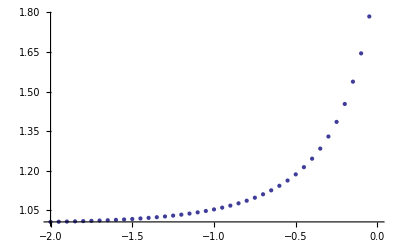

```mathematica
ListPlot[{#[[1]],#[[3]]}&/@Select[Operation[RawDataImport,1],#[[2]]==1.0&]]
```

```mathematica
Length[Select[Operation[RawDataImport,1],#[[2]]==-2&]]
```

40

```mathematica
ListDensityPlot[Operation[RawDataImport,1],InterpolationOrder->0,Mesh->None,PlotLegends->Automatic, ColorFunction->"Rainbow",PlotLabel->ParameterLabel[[1]]]
```

-Graphics-

```mathematica
ListDensityPlot[Operation[RawDataImport,2],InterpolationOrder->0,Mesh->None,PlotLegends->Automatic, ColorFunction->"Rainbow",PlotLabel->ParameterLabel[[2]]]
```

-Graphics-

```mathematica
xticks= Log10[Join[Table[x,{x,0.01,0.1,0.01}],Table[x,{x,0.1,1.0,0.1}]]];
yticks = Log10[Join[Table[x,{x,0.01,0.1,0.01}],Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1.0,10.0,1.0}],Table[x,{x,10.0,100.0,10.0}]]];
colors={RGBColor[41/255,162/255,198/255],RGBColor[255/255,109/255,49/255],RGBColor[255/255,203/255,24/255],RGBColor[115/255,182/255,107/255]};
MBData = Log10/@Import["/Users/carguelles/Workspace/IC_sterile/plots/MBLSND.txt","Data"];
```

```mathematica
ICLimit=ListContourPlot[Operation[DataSelect],PlotLegends->Automatic,InterpolationOrder->1,Contours->{2.3,6.18,11.83,19.33},ContourShading->None,ColorFunction->Blue,ContourStyle->{Directive[colors[[1]],Thick],Directive[colors[[2]],Thick],Directive[colors[[3]],Thick],Directive[colors[[4]],Thick]},FrameLabel->{"sin^22θ_24","Δm_41^2[eV^2]"},FrameStyle->None,FrameTicks->{Table[{y,If[y==-2 || y == -1 || y ==0||y==2,ToString[Round[10^y,0.001]],""]},{y,xticks}],Table[{y,If[y==1 || y == -1 ||y==-2||y ==0 || y ==2,ToString[Round[
10^y,0.001]],""]},{y,yticks}]},Epilog->{Gray,Opacity[0.5],FilledCurve[BSplineCurve[MBData,SplineClosed->True]],Opacity[1.0],Red,PointSize[Large],Point[MinLoc[DataSelect]]}]
```

-Graphics-

# OLD

```mathematica
CosTh={ -1,-0.958621,-0.917241,-0.875862,-0.834483,-0.793103,-0.751724,-0.710345,-0.668966,-0.627586,-0.586207,-0.544828,-0.503448,-0.462069,-0.42069,-0.37931,-0.337931,-0.296552,-0.255172,-0.213793,-0.172414,-0.131034,-0.0896552,-0.0482759,-0.00689655,0.0344828,0.0758621,0.117241,0.158621,0.2};
NuEnergy= {100 ,106.376, 113.16, 120.375, 128.051, 136.216, 144.902, 154.141, 163.97, 174.426, 185.548, 197.379, 209.965, 223.354, 237.596, 252.746, 268.862 ,286.006, 304.244, 323.644, 344.281, 366.234, 389.587, 414.429, 440.855, 468.966, 498.869, 530.679, 564.518, 600.514, 638.806, 679.54, 722.87, 768.964, 817.997, 870.156, 925.642, 984.665, 1047.45, 1114.24, 1185.29, 1260.87, 1341.27, 1426.8, 1517.78, 1614.56, 1717.51, 1827.03, 1943.53, 2067.46, 2199.29, 2339.52, 2488.7, 2647.4, 2816.21, 2995.78, 3186.81, 3390.01, 3606.18, 3836.12, 4080.73, 4340.94, 4617.74, 4912.19, 5225.42, 5558.61, 5913.06, 6290.1, 6691.19, 7117.85, 7571.72, 8054.53, 8568.13, 9114.47 ,9695.66, 10313.9, 10971.6, 11671.2, 12415.4, 13207 ,14049.2, 14945 ,15898 ,16911.7, 17990.1, 19137.2, 20357.5, 21655.6 ,23036.5, 24505.4, 26068, 27730.2 ,29498.4, 31379.4, 33380.3, 35508.8, 37773, 40181.6, 42743.7, 45469.3, 48368.6 ,51452.8, 54733.7, 58223.8, 61936.4, 65885.8, 70087 ,74556.1, 79310.2, 84367.4, 89747, 95469.7, 101557, 108033, 114922, 122250, 130045, 138337,147158, 156542, 166524, 177142, 188438 ,200453, 213235, 226832, 241296, 256682, 273050, 290461, 308982, 328684 ,349642 ,371937, 395654, 420883, 447720, 476269, 506638, 538944, 573310, 609867, 648755, 690122, 734128, 780940, 830736, 883708 ,940057, 10^6};
```